Kitaev Random Circuit |

The Modelpaclet:QuantumPlaybook/tutorial/KitaevRandomCircuit#516853239 | Simulationpaclet:QuantumPlaybook/tutorial/KitaevRandomCircuit#1068023573
Setting up the modelpaclet:QuantumPlaybook/tutorial/KitaevRandomCircuit#339587717 | Analysispaclet:QuantumPlaybook/tutorial/KitaevRandomCircuit#1487900726

Here, the effects of random measurements on the entanglement in the Kitaev chain of Majorana fermions is investigated. A realization of such Kitaev random circuit is shown in Figure 1.

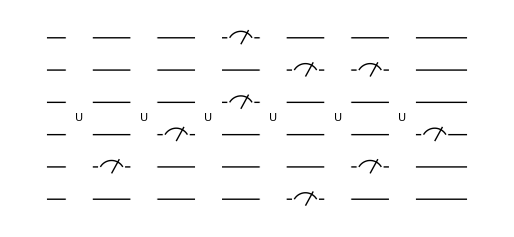

Figure 1. A typical form of Kitaev random circuit. Each line indicates a fermion mode, the unitary gate with label U denotes the time-evolution of Kitaev's model of Majorana fermions, and the measurement symbols depict the measurement of occupation number of the fermion modes.

This demonstration page was motivated by the phenomenon of measurement-induced entanglement transition, a transition between two distinct phases with the entanglement entropy characterized by area- and volume-law scaling. See also Li, Chen, and Fisher (2018)https://doi.org/10.1103%2Fphysrevb.98.205136, Skinner, Ruhman, and Nahum (2019)https://doi.org/10.1103%2Fphysrevx.9.031009, Chan et. al. (2019)https://doi.org/10.1103/PhysRevB.99.224307, Sang et al. (2021)https://doi.org/10.1103/PRXQuantum.2.030313, and Weinstein, Bao, and Altman (2022)https://doi.org/10.1103/PhysRevLett.129.080501.

WickStatepaclet:Q3/ref/WickStateQ3 Package Symbol | Represents a many-fermion quantum state for non-interacting fermions with pairing correlation
WickUnitarypaclet:Q3/ref/WickUnitaryQ3 Package Symbol | Unitary gate associated with a Bogoliubov-de Gennes type Hamiltonian
WickJumppaclet:Q3/ref/WickJumpQ3 Package Symbol | Non-unitary gate on BdG states
RandomWickCircuitSimulatepaclet:Q3/ref/RandomWickCircuitSimulateQ3 Package Symbol | Rancomd quantum circuit consisting of fermionic gates.
WickGreenFunctionpaclet:Q3/ref/WickGreenFunctionQ3 Package Symbol | Calculates the Green's functions with respect to a Wick state
WickEntanglementEntropypaclet:Q3/ref/WickEntanglementEntropyQ3 Package Symbol | Calculates the entanglement entropy in a Wick state
WickLogarithmicNegativitypaclet:Q3/ref/WickLogarithmicNegativityQ3 Package Symbol | Calculates the logarithmic negativity in a Wick state

Functions for fermionic quantum computation.

The Model

Make sure to load Q3.

```mathematica
<<Q3`
```

Set the number of fermion modes to consider.

```mathematica
$n=6;
```

Choose a specific set of fermion modes for conversion between the conventional and Wick representations.

```mathematica
Let[Fermion,c]
cc=c[Range@$n]
cccc=Join[cc,Dagger@cc];
```

{c_(,,1),c_(,,2),c_(,,3),c_(,,4),c_(,,5),c_(,,6)}

Construct the many-body Hamiltonian of the Kitaev chain (Kitaev, 2001)https://doi.org/10.1070/1063-7869/44/10S/S29.

```mathematica
HH=-μ*Q[cc]-t*PlusDagger[Hop@cc]+Δ*PlusDagger[Pair@cc]//Garner
```

-Graphics-

Examine the connectivity between neighboring fermion modes.

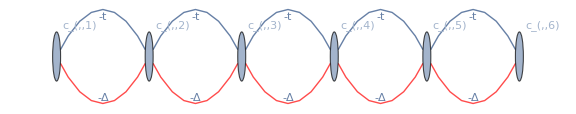

```mathematica
GraphForm[HH]
```

Extract the single-particle (or Bogoliubov-de Gennes) Hamiltonian (cf. many-body Hamiltonian in the above) of the model in the Nambu space. Notice the factor of 2.

```mathematica
barH=2*CoefficientTensor[HH,Dagger@cccc,cccc];
ArrayShort[barH,"Size"->8]
```

(-μ | -t | 0 | 0 | 0 | 0 | 0 | -Δ | …
-t | -μ | -t | 0 | 0 | 0 | Δ | 0 | …
0 | -t | -μ | -t | 0 | 0 | 0 | Δ | …
0 | 0 | -t | -μ | -t | 0 | 0 | 0 | …
0 | 0 | 0 | -t | -μ | -t | 0 | 0 | …
0 | 0 | 0 | 0 | -t | -μ | 0 | 0 | …
0 | Δ | 0 | 0 | 0 | 0 | μ | t | …
-Δ | 0 | Δ | 0 | 0 | 0 | t | μ | …
… | … | … | … | … | … | … | … | …)

Check that 1/2(c̲)^†H̲ c̲ reproduces the original Hamiltonian (up to a constant).

```mathematica
MultiplyDot[Dagger@cccc,barH.cccc]/2-HH//Garner
```

3 μ

To better understand the structure of the BdG Hamiltonian matrix, examine the single-particle and pairing blocks.

```mathematica
blocks=PartitionInto[barH,{2,2}];
ArrayShort[blocks]
```

((-μ | -t | 0 | 0 | …
-t | -μ | -t | 0 | …
0 | -t | -μ | -t | …
0 | 0 | -t | -μ | …
… | … | … | … | …) | (0 | -Δ | 0 | 0 | …
Δ | 0 | -Δ | 0 | …
0 | Δ | 0 | -Δ | …
0 | 0 | Δ | 0 | …
… | … | … | … | …)
(0 | Δ | 0 | 0 | …
-Δ | 0 | Δ | 0 | …
0 | -Δ | 0 | Δ | …
0 | 0 | -Δ | 0 | …
… | … | … | … | …) | (μ | t | 0 | 0 | …
t | μ | t | 0 | …
0 | t | μ | t | …
0 | 0 | t | μ | …
… | … | … | … | …))

Setting up the model

Make sure to load Q3.

```mathematica
<<Q3`
```

Set the number of fermion modes to consider.

```mathematica
$n=10;
```

Set the parameters.

```mathematica
μ=0.2;
t=Δ=1;
```

Directly construct the BdG Hamiltonian matrix (without using the fermion operator algebra as in the above section).

```mathematica
hrm=-μ*One[$n]-t*PlusTopple@One[{$n,$n},1];
del=-Δ*One[{$n,$n},1];
del=del-Transpose[del];
ham=NambuHermitian[{hrm,del}];
ham//ArrayShort
```

{(-0.2 | -1 | 0 | 0 | …
-1 | -0.2 | -1 | 0 | …
0 | -1 | -0.2 | -1 | …
0 | 0 | -1 | -0.2 | …
… | … | … | … | …),(0 | -1 | 0 | 0 | …
1 | 0 | -1 | 0 | …
0 | 1 | 0 | -1 | …
0 | 0 | 1 | 0 | …
… | … | … | … | …)}

The time interval for each unitary layer to operate.

```mathematica
$τ=3.;
```

Construct the single-particle unitary matrix.

```mathematica
uv=NambuUnitary@MatrixExp[-I*Normal[ham]]
```

NambuUnitary[…]

You can use the above unitary matrix in the Dirac spinor space (also known as the Nambu space). But it is slightly faster to first convert it to the equivalent matrix in the Majorana spinor space.

```mathematica
wu=WickUnitary[uv]
```

WickUnitary[…]

Prepare an initial state. A half-filling is a common choice.

```mathematica
in=WickState[{1,0},$n]
```

WickState[…]

The probability to perform a measurement on each fermion mode.

```mathematica
$p=.2;
```

The depth of quantum circuit.

```mathematica
$T=20; (* must be an integer *)
```

Simulation

The simulation involves a lot of random number generators. To get the same result every time you open this document, set the seed of the random number generator.

```mathematica
SeedRandom[354];(*for tests*)
```

Construct 10 random circuits and run each circuit 5 times. Notice the "Samples"→{10,5} option.

```mathematica
EchoTiming[
{data,qc}=RandomWickCircuitSimulate[in,{wu,$p},$T,"Samples"->{200,2}];
]
```

3.53166

Examine the output data format: There are 10 entries because the same number of quantum circuits were randomly generated.

```mathematica
Length[qc]
```

200

```mathematica
Dimensions[data]
```

{200,2,41}

If you want, examine the circuits by displaying them in a graphical form.

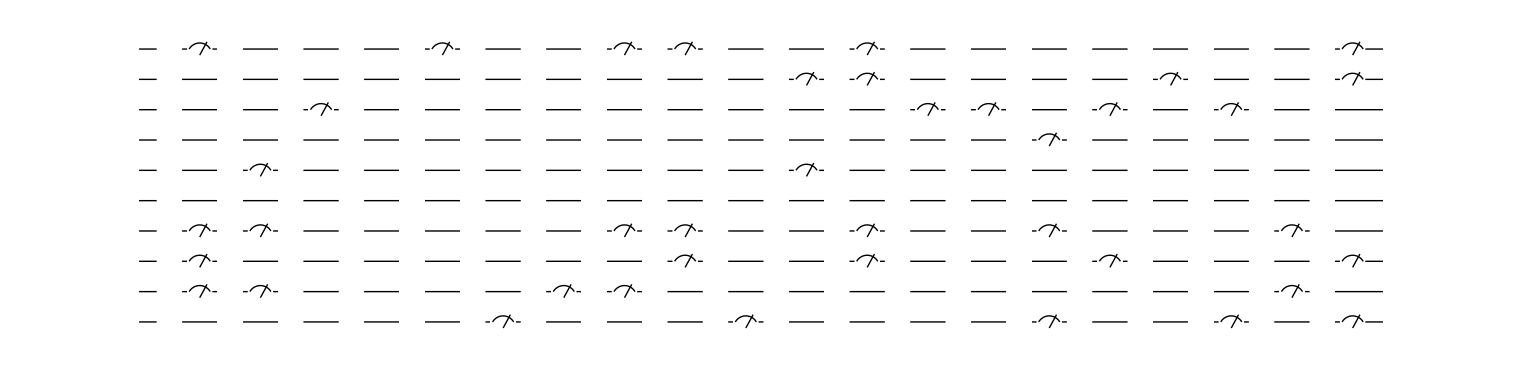

```mathematica
Show[qc[[2]]]
```

Examine some of the output states as well.

```mathematica
out=data[[2,2,3]]
```

WickState[…]

Analysis

Each entry in the converted data wcs contains the information about one realization of quantum trajectory. Extract the trajectory history in an explicit form, for example, of the first entry.

```mathematica
trj=Flatten[data,1][[;;,1;;;;2]];
```

In this particular case, there are 13 entries; the first entry is just the initial state and the rest are corresponds to the layers; there are 6 layers and each layer contains two sublayers of unitary evolution and measurements.

```mathematica
Dimensions[trj]
```

{400,21}

Note that the output states are all normalized.

```mathematica
EchoTiming[nrm=Map[NormSquare,trj,{2}];]
ArrayShort[nrm]
```

0.008658

(1 | 1 | 1 | 1 | …
1 | 1 | 1 | 1 | …
1 | 1 | 1 | 1 | …
1 | 1 | 1 | 1 | …
… | … | … | … | …)

```mathematica
nrm-1//ArrayZeroQ
```

True

### Green's functions

For non-interacting fermion modes, most physical properties may be obtained from single-particle Green's functions. It is a good idea to calculate the Green's functions first.

Calculate the Green's functions between all fermion modes.

```mathematica
EchoTiming[grn=WickGreenFunction[trj]];
```

1.13405

```mathematica
Dimensions[grn]
```

{400,21}

```mathematica
grn[[1,3]]
```

NambuGreen[…]

### Entanglement Entropy

For further analysis, take the subsystem. Below, we will consider entanglement properties between this subsystem and the rest.

```mathematica
aa=Range[$n/2]
```

{1,2,3,4,5}

Calculate the entanglement entropy.

```mathematica
EchoTiming[ee=Map[WickEntanglementEntropy[aa],grn,{2}];]
```

2.00197

Take the average of the entanglement entropy over different trajectories, and plot it as a function of time.

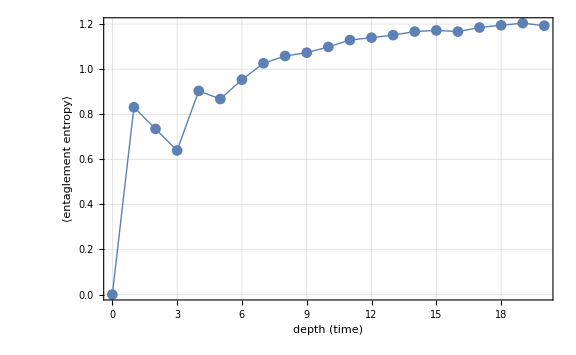

```mathematica
ListLinePlot[Mean[ee],
DataRange->{0,$T},
PlotMarkers->Automatic,
FrameLabel->{"depth (time)", "⟨entaglement entropy⟩"}]
```

### Logarithmic Negativity

For further analysis, take the subsystem. This has been defined above; just in case.

```mathematica
aa=Range[$n/2]
```

{1,2,3,4,5}

At the moment, the current implementation of WickLogarithmicNegativity does not handle trivial cases of Green’s function, which internally lead to singular matrices. To avoid such cases, put a small value to the “Epsilon” option.

```mathematica
SetOptions[WickLogarithmicNegativity,"Epsilon"->1.25*^-5]
```

{Epsilon→0.0000125}

Calculate the logarithmic negativity of each state in the particular trajectory.

```mathematica
EchoTiming[neg=Re@Map[WickLogarithmicNegativity[aa],grn,{2}];]
```

12.8091

Plot the entanglement (logarithmic negativity) of the first trajectory.

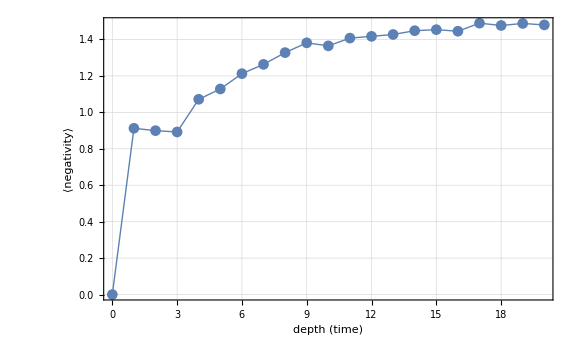

```mathematica
ListLinePlot[Mean[neg],
PlotRange->All,
DataRange->{0,$T},
PlotMarkers->Automatic,
FrameLabel->{"depth (time)", "⟨negativity⟩"}]
```

| Related Guides
▪Fermionic Quantum Computation
▪Quantum Many-Body Systems
▪Q3

| Related Tech Notes
▪A Quantum Playbook
▪Quantum Many-Body Systems with Q3
▪Q3: Quick Start

| Related Links
▪B. M. Terhal and D. P. DiVincenzo (2002)https://doi.org/10.1103/PhysRevA.65.032325, Physical Review A 65, 032325, "Classical simulation of noninteracting-fermion quantum circuits."
▪A. Yu. Kitaev (2001)https://doi.org/10.1070/1063-7869/44/10S/S29, Physics-Uspekhi 44, 131 (2001), "Unpaired Majorana fermions in quantum wires." 
▪Y. Li, X. Chen, and M. P. A. Fisher (2018)https://doi.org/10.1103%2Fphysrevb.98.205136, Physical Review B 98, 205136 (2018), "Quantum Zeno effect and the many-body entanglement transition."
▪B. Skinner, J. Ruhman, and A. Nahum (2019)https://doi.org/10.1103%2Fphysrevx.9.031009, Physical Review X 9, 031009 (2019), "Measurement-Induced Phase Transitions in the Dynamics of Entanglement."
▪A. Chan et. al. (2019)https://doi.org/10.1103/PhysRevB.99.224307, Physical Review B 99, 224307 (2019), "Unitary-projective entanglement dynamics."
▪S. Sang et al. (2021)https://doi.org/10.1103/PRXQuantum.2.030313, PRX Quantum 2, 030313 (2021), "Entanglement Negativity at Measurement-Induced Criticality."
▪Z. Weinstein, Y. Bao, and E. Altman (2022)https://doi.org/10.1103/PhysRevLett.129.080501, Physical Review Letters 129, 080501 (2022), "Measurement-Induced Power-Law Negativity in an Open Monitored Quantum Circuit."
▪Mahn-Soo Choi (2022)https://doi.org/10.1007/978-3-030-91214-7, A Quantum Computation Workbook (Springer).
▪About Q3